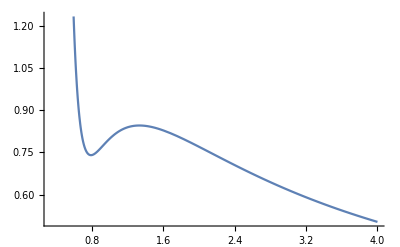

```mathematica
p[t_,v_]:=(8*t)/(3*v-1)-3/(v^2)
Plot[p[.95,v],{v,1/3,4}]
```

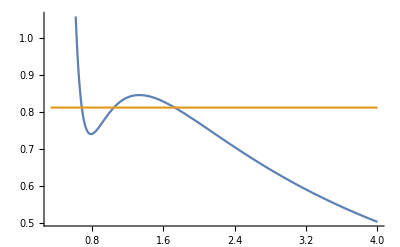

```mathematica
Plot[{p[.95,v],.812},{v,1/3,4}]
```

```mathematica
{v01,v02,v03}=Values[NSolve[(8*.95)/(3*v-1)-3/(v^2)==.8119,v]]
```

{{1.72692},{1.04255},{0.684111}}

```mathematica
Integrate[.8119-(8*.95)/(3*v-1)+3/(v^2),{v,v01[[1]],v02[[1]]}]-Integrate[(8*.95)/(3*v-1)-3/(v^2)-.8119,{v,v02[[1]],v03[[1]]}]
```

-0.0000216467

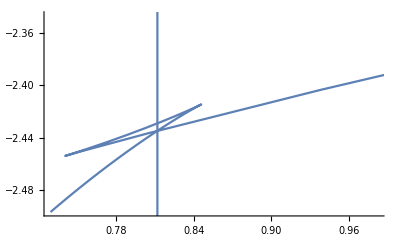

```mathematica
G[v_,t_]:=-t*Log[3*v-1]+t/(3*v-1)-9/(4*v)
plot1=ParametricPlot[{p[.95,v],G[v,.95]},{v,0,2.25}];
plot2=ParametricPlot[{.8119,t},{t,0,-10}];
Show[{plot1,plot2}]
```

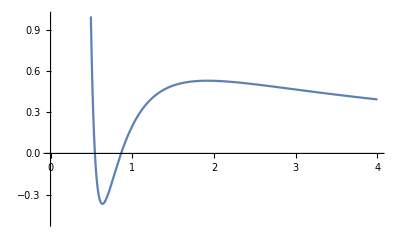

```mathematica
Plot[p[.8,v],{v,1/3,4},PlotRange->{-.5,1}]
```

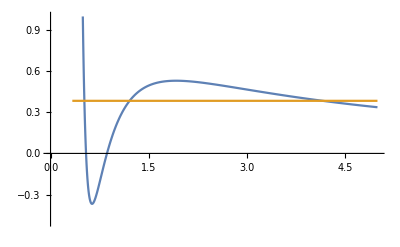

```mathematica
Plot[{p[.8,v],.384},{v,1/3,5},PlotRange->{-.5,1}]
```

```mathematica
p1=.3833
{v11,v12,v13}=Values[NSolve[(8*.8)/(3*v-1)-3/(v^2)==p1,v]]
Integrate[p1-(8*.8)/(3*v-1)+3/(v^2),{v,v11[[1]],v12[[1]]}]-Integrate[(8*.8)/(3*v-1)-3/(v^2)-p1,{v,v12[[1]],v13[[1]]}]
```

0.3833

{{4.17345},{1.20817},{0.517412}}

0.000225268

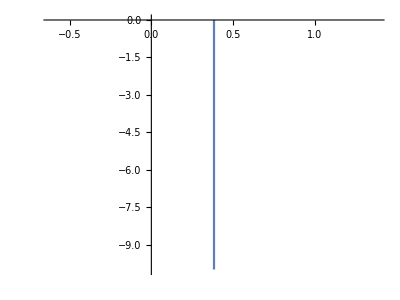

```mathematica
ParametricPlot[{p[.8,v],G[v,.8]},{v,0,10}];
plot2=ParametricPlot[{.3833,t},{t,0,-10}];
Show[{plot1,plot2}]
```